Cómo escribir código de buena calidad

En cierto modo, escribir código de buena calidad es parecido a escribir prosa de buena calidad: hay que tener las ideas claras y, además, expresarlas con corrección. Quien se inicia en la programación frecuentemente piensa en español, o cualquiera que sea su lengua, lo que quiere que haga su programa. Sin embargo, a medida que se adquiere desenvoltura en el uso de Wolfram Language, se hará un hábito pensar directamente en términos de código, lo que hará más fácil escribir un programa que describir su intención.

Mi objetivo como diseñador de Wolfram Language ha sido que la expresión de cualquier cosa sea lo más fácil posible. Los nombres de las funciones en Wolfram Language son muy semejantes a las palabras en lenguaje natural, y he hecho grandes esfuerzos para escogerlos de manera adecuada.

Funciones tales como Table o NestList o FoldList existen en Wolfram Language porque se refieren a acciones que se efectúan frecuentemente. Tal y como pasa con el lenguaje natural, suele haber diferentes maneras de expresar lo mismo, pero si se quiere lograr código de buena calidad hay que encontrar la que resulte más directa y más sencilla.

Así, para crear una tabla con los 10 primeros cuadrados hay, en Wolfram Language, una porción obvia de buen código que no usa más que la función Table.

Código en Wolfram Language, sencillo y de buena calidad, para formar la tabla de los 10 primeros cuadrados:

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

¿Qué necesidad habría de escribir algo diferente? Frecuentemente, no se piensa en la “tabla completa”, sino en los pasos que habría que seguir para construirla. En las primeras épocas de la era de la computación, las máquinas necesitaban de toda la ayuda que el programador pudiera darles, y la única opción era mediante un código que describiera paso a paso lo que tenían que hacer.

Aquí se ve un código, mucho menos pulcro, que construye la tabla paso a paso:

```mathematica
Module[{list,i}, list={}; For[i=1,i≤10,i++, list=Append[list,i^2]];list]
```

{1,4,9,16,25,36,49,64,81,100}

Wolfram Language permite expresar las cosas a un nivel más alto, y crear código que atrape la idea lo más directamente que se pueda. Una vez que se conoce el lenguaje, será mucho más eficiente operar en ese nivel y, así, escribir código más fácil de entender, tanto por las computadoras como por los seres humanos.

Para escribir código de buena calidad, es muy importante preguntarse con frecuencia, “¿cuál es el escenario completo de lo que este código pretende lograr?” Muchas veces, cuando se comienza a tratar con algún problema, se entiende solo una parte, y se escribe el código específicamente para eso. Y luego, poco a poco, se extiende, añadiéndose más y más porciones. En cambio, al reflexionar en términos del escenario completo, de pronto se da uno cuenta de que existe alguna función poderosa, como Fold, a la que se puede recurrir para simplificar y hacer que el código sea otra vez pulcro y sencillo.

Escriba un código para convertir los dígitos de {centenas,decenas,unidades} en un solo entero:

```mathematica
fromdigits[{h_,t_,o_}]:=100h+10t+o
```

Ejecute el código:

```mathematica
fromdigits[{5,6,1}]
```

561

Ahora, se generaliza lo anterior a una lista de cualquier longitud, usando Table:

```mathematica
fromdigits[list_List]:=Total[Table[10^(Length[list]-i)*list[[i]],{i,Length[list]}]]
```

Este nuevo código funciona:

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

A continuación, se simplifica el código multiplicando la lista completa de potencias de 10 al mismo tiempo:

```mathematica
fromdigits[list_List]:=Total[10^Reverse[Range[Length[list]]-1]*list]
```

Se borran las definiciones previas y se intenta un nuevo enfoque de tipo recursivo:

```mathematica
Clear[fromdigits]
```

```mathematica
fromdigits[{k_}]:=k
```

```mathematica
fromdigits[{digits___,k_}]:=10*fromdigits[{digits}]+k
```

Este nuevo enfoque también funciona:

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

Pero en este punto se da uno cuenta de que, en efecto, ¡se trata de un simple Fold!

```mathematica
Clear[fromdigits]
```

```mathematica
fromdigits[list_]:=Fold[10*#1+#2&,list]
```

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

Y, por supuesto, también hay una función nativa que hace lo mismo:

```mathematica
FromDigits[{5,6,1,7,8}]
```

56178

¿Por qué conviene que el código de buena calidad sea simple? Primero, porque es más probable que esté correcto. Es mucho más fácil que algún error se produzca en un código complicado que en uno simple. Además, un código simple es casi siempre más general y, por tanto, tiende a cubrir casos que ni siquiera se habían considerado al principio y, así, se evitará tener que incorporar más y más código. Y, por último, un código simple es mucho más fácil de leer y entender. (Más simple no es sinónimo de más breve y, de hecho, hay códigos muy breves que pueden ser muy complicados de entender).

Una versión excesivamente abreviada de fromdigits, que ya es un poco difícil de entender:

```mathematica
fromdigits =Fold[{10,1}.{##}&,#]& ;
```

Aunque, claro, sí que funciona:

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

Si lo que se quiere hacer es complicado, es muy posible que el código sea también complicado. Sin embargo, un código de buena calidad se puede subdividir en funciones y definiciones tan simples y autocontenidas cuanto sea posible. Y, así, aun en programas muy largos escritos en Wolfram Language, casi no se encontrarán definiciones que requieran más allá de unas cuantas líneas.

He aquí una sola definición en la que se combinan varios casos:

```mathematica
fib[n_]:=If[!IntegerQ[n]||n<1,"Error",If[n==1||n==2,1,fib[n-1]+fib[n-2]]]
```

Es mucho mejor subdividirla en varias definiciones más simples:

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_Integer]:=fib[n-1]+fib[n-2]
```

Una cuestión muy importante al escribir código de buena calidad es la buena selección de nombres para las funciones. En las funciones nativas de Wolfram Language he hecho grandes esfuerzos, a lo largo de varias décadas, para escoger bien sus nombres, y captar en forma breve la esencia de lo que hacen y de cómo se piensa en ellas.

Al estar escribiendo algún programa, sucede que hay que definir una nueva función porque se necesita en un contexto muy específico. Pero siempre vale la pena tratar de darle un nombre que se entienda fuera de ese contexto. Porque muchas veces, si no se le encuentra un buen nombre, es señal de que quizá no sea la función que haya que definir.

Una indicación de que el nombre de una función es bueno es que, al toparse con él en algún código, inmediatamente se puede saber lo que hace. Y, ciertamente, una característica importante de Wolfram Language es que a menudo es más fácil seguir y entender directamente un código bien escrito, que cualquier descripción textual que se quiera hacer del mismo.

¿Cómo describir lo siguiente en lenguaje llano?

```mathematica
Graphics[{White,Riffle[NestList[Scale[Rotate[#,0.1],0.9]&,Rectangle[ ],40],{Pink,Yellow}]}]
```

-Graphics-

Al escribir algún programa en Wolfram Language, puede presentarse el dilema entre usar una función nativa, tal vez algo rara, pero que hace exactamente lo que uno quiere, o bien, llegar a la misma funcionalidad, pero utilizando varias funciones más conocidas. Y, sí, a veces he tratado en este libro de evitar el uso de funciones raras para minimizar el vocabulario. Pero el código de mejor calidad tiende a usar funciones únicas siempre que se pueda, puesto que el nombre de la función explica su intención de mejor manera de lo que se lograría si se usan varias diferentes.

Use un código breve para invertir los dígitos de un entero:

```mathematica
FromDigits[Reverse[IntegerDigits[123456]]]
```

654321

Pero hay una función nativa cuyo nombre describe más claramente su intención:

```mathematica
IntegerReverse[123456]
```

654321

El código de buena calidad debe ser correcto y fácil de entender. Pero también debe ser eficiente al ejecutarse. Y, en Wolfram Language, usualmente el código simple es también mejor en ese aspecto; y la razón es que, al explicar las intenciones con mayor claridad, Wolfram Language puede optimizar con más facilidad los cómputos que debe hacer internamente.

En cada nueva versión, Wolfram Language ha ido mejorando su capacidad para encontrar automáticamente la manera de ejecutar un código con mayor rapidez. Aunque, claro, siempre ayuda que los algoritmos que se vayan a usar tengan una buena estructuración.

Timing reporta el tiempo utilizado en un cómputo (en segundos), además del resultado:

```mathematica
Timing[fib[20]]
```

{0.021843,6765}

Grafique el tiempo usado en el cómputo de fib[n] según las definiciones dadas anteriormente.

Con las definiciones de arriba para fib, el tiempo utilizado crece muy rápidamente:

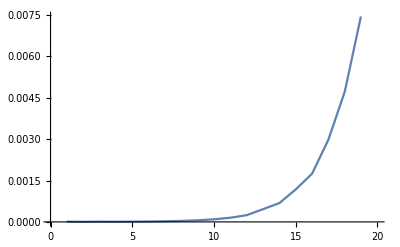

```mathematica
ListLinePlot[Table[First[Timing[fib[n]]],{n,20}]]
```

Sucede que el algoritmo utilizado realiza una cantidad exponencial de trabajo innecesario, pues recalcula una y otra vez lo que ha sido calculado previamente. Esto puede evitarse si se hace una asignación para fib[n] cuando se hace la definición de fib[n_], de tal modo que se vaya almacenando el resultado de cada cómputo intermedio.

Redefina la función fib de modo tal que recuerde cada valor que vaya calculando:

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_Integer]:=fib[n]=fib[n-1]+fib[n-2]
```

En este caso, hasta el 1000, se ve que cada nuevo valor se obtiene en unos cuantos microsegundos:

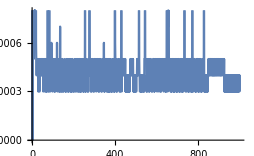

```mathematica
ListLinePlot[Table[First[Timing[fib[n]]],{n,1000}]]
```

Vocabulario

FromDigits[list] |   | arma un entero a partir de sus dígitos
IntegerReverse[n] |   | invierte el orden de los dígitos de un entero
Timing[expr] |   | efectúa un cálculo, e incluye el tiempo que toma en hacerlo

"5 Exercises Available" | "Get Started »"

Encuentre una forma más simple para Module[{a,i},a=0; For[i=1,i≤1000,i++,a=i*(i+1)+a];a]. »

| Expected output: |  
  | 334334000 |

Encuentre una forma más simple para Module[{a,i},a=x; For[i=1,i≤10,i++, a=1/(1+a)];a]. »

| Expected output: |  
  | 1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x)))))))))) |

Encuentre una forma más simple para Module[{i,j,a},a={}; For[i=1,i≤10,i++,For[j=1,j≤10,j++,a=Join[a,{i,j}]]];a]. »

| Expected output: |  
  | {1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10} |

Obtenga el gráfico con los puntos unidos del tiempo usado para realizar en el cálculo de n^n, para n hasta 10 000. »

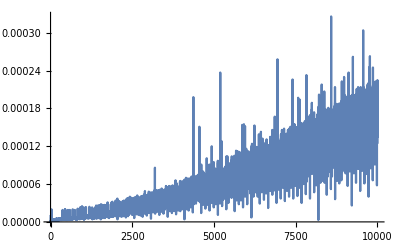
| Expected output: |  
  | -Graphics- |

Produzca la gráfica con los puntos unidos del tiempo usado por Sort para ordenar Range[n] en orden aleatorio, para n hasta 200. »

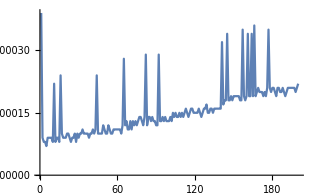
| Sample expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Qué significa i++?

Es la notación abreviada para i=i+1. Es la misma notación utilizada por C y muchos otros lenguajes de bajo nivel para indicar esta operación de incremento.

¿Qué hace la función For?

Se trata del análogo directo del comando for(...) en C. For[start,test,step,body] ejecuta, primero, start, luego hace la prueba test, enseguida ejecuta step, y luego body. Hace esto repetidamente hasta test ya no da True.

¿Por qué algunas porciones abreviadas de código pueden ser difíciles de entender?

Lo más frecuente es que se han ido eliminando variables, y aun funciones, de manera que al final quedan muy pocos nombres para leerse, que son los que podrían dar alguna indicación de lo que supuestamente intenta hacer el código.

¿Cuál es el mejor IDE (entorno de desarrollo integrado) para escribir código en Wolfram Language?

Para la programación cotidiana, lo mejor es usar los cuadernos de Wolfram. Es importante usar secciones, texto y ejemplos junto con el código. En proyectos grandes de software, con múltiples desarrolladores, Wolfram Workbench contiene un IDE basado en Eclipse.

¿Qué es lo que mide Timing?

Mide el tiempo de CPU usado dentro de Wolfram Language para el cómputo del resultado. No toma en cuenta el tiempo usado para mostrar en pantalla el resultado. Tampoco incluye el tiempo usado en operaciones externas, tal como traer información de la nube. Si se quiere el tiempo total absoluto, el que mediría un reloj común y corriente, habrá que usar AbsoluteTiming.

¿Cómo se obtienen mediciones de tiempo más precisas en el caso de códigos que corren muy rápido?

Use RepeatedTiming, que corre el mismo código muchas veces y promedia los tiempos resultantes. (Esto no funciona cuando el código se modifica a sí mismo, como en la última definición de fib que se dio más arriba).

¿Qué trucos hay para acelerar el código?

Además de esforzarse por mantener el código simple, uno de ellos es no recalcular nada que ya haya sido calculado. También puede mencionarse que, cuando se tienen muchos números, puede ser una buena idea usar N para que los números estén en forma aproximada. En algunos algoritmos internos se puede escoger el PerformanceGoal deseado y lograr un equilibrio entre velocidad y exactitud. Existen, además, funciones tales como Compile que tienen como propósito que gran parte del trabajo asociado a la optimización se realice por separado, de manera mucho más rápida que si se hiciera durante el cómputo propiamente.

Notas técnicas

Pueden generarse comportamientos muy complicados, aun usando código muy simple; de eso trata mi libro, de 1280 páginas, A New Kind of Science. Ahí se puede encontrar un buen ejemplo de lo anterior: CellularAutomaton[30,{{1},0}].

La función fib efectúa el cálculo de Fibonacci[n]. La definición original siempre lleva un proceso recurrente a través de un árbol de valores descendentes O(ϕ^n), donde ϕ≈1.618 es la razón áurea (GoldenRatio).

La capacidad de recordar valores que hayan sido calculados previamente por alguna función se llama a veces memoización, a veces programación dinámica y, a veces, simplemente cacheado.

La función IntegerReverse se introdujo en la Version 10.3.

Cuando se trata de programas grandes, Wolfram Language tiene un marco estructural para poder aislar funciones dentro de contextos y paquetes.

If[#1>2,2#0[#1-#0[#1-2]],1]&/@Range[50] es un ejemplo de código abreviado que presenta un reto serio para entender lo que quiere decir.